## Write Data to files.

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

Test Legend fuctioning.

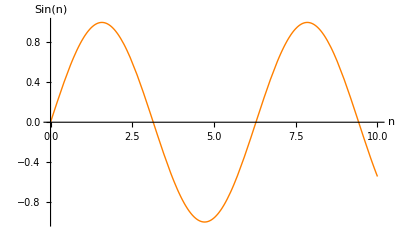

```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
tranzs=31 ;tranzDE1=23;tranzDE2=23;tranzL=23;
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
norts=138-tranzs;nortL=138-tranzL;nort1=138-tranzDE1;nort2=138-tranzDE2;
(*k1,k2 should not equal to kDE1 at first. Should keep this when calculating!!!!*)
(**************************)
Print[Style["Test Legend fuctioning.",30,Bold,Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Parameters",30,Bold,Orange]]
(*********************************************)
wL=-1;
w1 =-1.1;
w2=-1.2;
δ2=-0.000001;
ΩDE0 =0.73;
Ωk0=0;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
h=0.71;
ce2 = 0.1
(*h=1;*)
 (*H0 =(100 h)/300000;*)
H0=100 h;(*the real value is not very important here. this means all length units are MPc/h, all wavenumber units are h/MPc*)
Ωm0s =1; 
Ωr0s =8.09*10^-5;
(*Ωr0s=0;*)
nzs=nzL=nz2=nz3=nz4=aeq=Ωr0/Ωm0
c=300000
```

Parameters

0.1

0.00029963

300000

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at early time",30,Bold,Orange]]
(*********************************************)
HL0=H10=H20=H0;
Hs0=H0;
```

Intial conditions for Hubble constant, normalized at early time

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",30,Bold,Orange]]
(*********************************************)
Hs[a_]:= Hs0  √(Ωr0s a^-4+Ωm0s a^-3);mHs[a_]=a Hs[a];
HL[a_]:= HL0  √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0);mHL[a_]=a HL[a];
H1[a_]:= H10 √(Ωr0 a^-4+Ωm0 a^-3+1/(δ2+w1)ΩDE0 a^-3(δ2+w1 a^(-3(δ2+w1))));mH1[a_]=a H1[a];
H2[a_]:= H20 √(Ωr0 a^-4+Ωm0 a^-3+ 1/(δ2+w2)ΩDE0 a^-3(δ2+w2 a^(-3(δ2+w2))));mH2[a]=a H2[a];
iHs[a_]:= Hs0  √(Ωm0s a^-1);
iHL[a_]:= HL0  √(Ωm0 a^-1+1/(δ2+wL)ΩDE0 a^-3(δ2+wL a^(-3(δ2+wL))))
iH1[a_]:= H10 √(Ωm0 a^-1+ 1/(δ2+w1)ΩDE0 a^-1(δ2+w1 a^(-3(δ2+w1))))
iH2[a_]:= H20 √(Ωm0 a^-1+  1/(δ2+w2)ΩDE0 a^-1(δ2+w2 a^(-3(δ2+w2))))
```

Define Hubble functions

```mathematica
(*********************************************)
Print[Style["Particle Horizon",30,Bold,Orange]]
(*********************************************)
dHs[a_?NumberQ]:=c a NIntegrate[1/(Hs[x] x^2),{x,0,a}];
dHL[a_?NumberQ]:=c a NIntegrate[1/(HL[x] x^2),{x,0,a}];
dH1[a_?NumberQ]:=c a NIntegrate[1/(H1[x] x^2),{x,0,a}];
dH2[a_?NumberQ]:=c a NIntegrate[1/(H2[x] x^2),{x,0,a}];
```

Particle Horizon

```mathematica
(*********************************************)
Print[Style["Define k of a",30,Bold,Orange]]
(*********************************************)
kL[a_]:= 1/dHL[a];ks[a_]:= 1/dHs[a];kDE1[a_]:= 1/dH1[a];kDE2[a_]:=1/dH2[a];
1/dHL[0.01]
{keqL=1/dHL[aeq],keq1=1/dH1[aeq],keq2=1/dH2[aeq]}
{k0L=1/dHL[1],k01=1/dH1[1],k02=1/dH2[1]}
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

0.0730456

{28.6212,28.6212,28.6212}

{0.0000699507,0.0000693324,0.0000688092}

```mathematica
(*********************************************)
Print[Style["Define growth factors",30,Bold,Orange]]
(*********************************************)
(*
I am not sure what initial conditions to impose. So I just tried the adiabatic initial condition that says Subscript[δ, de]=1/4 Subscript[δ, γ], Subscript[θ, de]=Subscript[θ, γ]
*)
λ1[a_]=(ΩDE0  a^(-3(δ2 +w1)))/(Ωm0+δ2/(δ2+w1)ΩDE0(1-a^(-3(δ2+w1))));
λ2[a_]=(ΩDE0  a^(-3(δ2 +w2)))/(Ωm0+δ2/(δ2+w2)ΩDE0(1-a^(-3(δ2+w2))));
Growths[a_]:= 5/2 Ωm0s  Hs[a]/Hs0 NIntegrate[1/(iHs[x]/Hs0)^3,{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,a}];
```

Define growth factors

Import power spectrum of LCDM calculated by cmbeasy, and some test

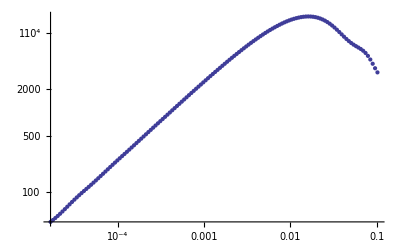

0.0000167287

0.000112794

281.02

138

0.0000118774==71. √(0.73+0.0000809/aL^4+0.27/aL^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

{}

{a1→4.72358}

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",30,Bold,Orange]]
(*********************************************)
PowerS=Import["cdm_11-27_cut.dat"];
ListLogLogPlot[PowerS]
(*The k in PowerS is in unit of h MPc^-1. Be careful when calculating.*)
PowerS[[1,1]]
PowerS[[tranzs]][[1]]
PowerS[[tranzs]][[2]]
leth=Length[PowerS]
PowerS[[1,1]]h== HL[aL]
Solve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h==H1[a1],a1,Reals]
FindRoot[PowerS[[1,1]]h==kDE1[a1],{a1,0.0001}]
```

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",30,Bold,Orange]]
(*********************************************)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
```

Tests for Hubble equations

100.004

52734.3

1.87323×10^6

1.03875×10^8

9.1433×10^9

9.00944×10^11

```mathematica
(*Once done, can be imported easily.*)
```

```mathematica
aokTabs11=Table[as/.FindRoot[PowerS[[i,1]]h==ks[as],{as,0.0001}],{i,1,leth}]
Export["DEInteracting\\2012-02-01\\aokTabs11.xls",aokTabs11,"XLS"]
aokTabL11=Table[aL/.FindRoot[PowerS[[i,1]]h==kL[aL],{aL,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabL11.xls",aokTabL11,"XLS"]
aokTabDE111=Table[a1/.FindRoot[PowerS[[i,1]]h==kDE1[a1],{a1,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabDE111.xls",aokTabDE111,"XLS"]
aokTabDE211=Table[a2/.FindRoot[PowerS[[i,1]]h==kDE2[a2],{a2,0.0001}],{i,1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabDE211.xls",aokTabDE211,"XLS"]
```

{4.643,4.45047,4.26594,4.08906,3.91952,3.75701,3.60125,3.45195,3.30884,3.17167,3.04019,2.91417,2.79337,2.67759,2.56661,2.46023,2.35827,2.26054,2.16686,2.07707,1.991,1.9085,1.82942,1.75362,1.68097,1.61133,1.54458,1.4806,1.41927,1.36048,1.30414,1.25012,1.19835,1.14873,1.10116,1.05557,1.01186,0.969971,0.929815,0.891325,0.854431,0.819066,0.785167,0.752673,0.721527,0.691671,0.663053,0.635621,0.609326,0.584121,0.55996,0.536801,0.514601,0.493321,0.472923,0.453371,0.434628,0.416662,0.39944,0.382931,0.367107,0.351938,0.337397,0.323458,0.310097,0.297289,0.285012,0.273243,0.261961,0.251146,0.240779,0.230841,0.221315,0.212183,0.203429,0.195037,0.186992,0.179281,0.171888,0.164802,0.158008,0.151496,0.145253,0.139268,0.133531,0.128031,0.122758,0.117704,0.112858,0.108213,0.10376,0.0994909,0.0953982,0.0914747,0.0877133,0.0841073,0.0806502,0.077336,0.0741586,0.0711125,0.0681922,0.0653924,0.0627082,0.0601349,0.0576677,0.0553024,0.0530347,0.0508605,0.048776,0.0467775,0.0448614,0.0430243,0.041263,0.0395743,0.0379551,0.0364027,0.0349143,0.0334872,0.0321189,0.0308069,0.0295489,0.0283427,0.0271862,0.0260773,0.025014,0.0239944,0.0230168,0.0220793,0.0211804,0.0203185,0.019492,0.0186994,0.0179394,0.0172106,0.0165117,0.0158416,0.0151989,0.0145826}

DEInteracting\2012-02-01\aokTabs11.xls

DEInteracting\2012-02-01\aokTabL11.xls

$Aborted

DEInteracting\2012-02-01\aokTabDE111.xls

$Aborted

DEInteracting\2012-02-01\aokTabDE211.xls

```mathematica
kDE1[1]
kDE2[1]
```

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",30,Bold,Orange]]
(*********************************************)
(*Manually set the start point(a≤1) of this table.*)(*Moved to the beginning of the file.*)
(*tranzs=43;tranzL=43;tranzDE2=43;tranzDE3=43;tranzDE4=43;*)
(********)
aokTabs=Table[as/.FindRoot[PowerS[[i,1]]h==ks[as],{as,0.0001}],{i,tranzs+1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabs.xls",aokTabs,"XLS"]
aokTabL=Table[aL/.FindRoot[PowerS[[i,1]]h==kL[aL],{aL,0.0001}],{i,tranzL+1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabL.xls",aokTabL,"XLS"]
aokTabDE1=Table[a1/.FindRoot[PowerS[[i,1]]h==kDE1[a1],{a1,0.0001}],{i,tranzDE1+1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabDE1.xls",aokTabDE1,"XLS"]
aokTabDE2=Table[a2/.FindRoot[PowerS[[i,1]]h==kDE2[a2],{a2,0.0001}],{i,tranzDE2+1,leth}];
Export["DEInteracting\\2012-02-01\\aokTabDE2.xls",aokTabDE2,"XLS"]
(*Check the results*)
aokTabs[[1]]
Length[aokTabL]
Length[aokTabs]
Length[aokTabDE1]
Length[aokTabDE2]
aokTabs
aokTabL
aokTabDE1
aokTabDE2
```

```mathematica
(*********************************************)
Print[Style["Plot k of a",30,Bold,Orange]]
(*********************************************)
ks[1]
kL[1]
kDE1[1]
kL[3*10^-4]
LogLogPlot[{ks[a],kL[a],kDE2[a]},{a,0.9,1.1},PlotStyle->{Red,Orange,Yellow}]
```

```mathematica
(*Finished dealing with k~a relations.*)
```

```mathematica
aokTabs111=Import["DEInteracting\\2012-02-01\\aokTabs11.xls"];
aokTabs11=Table[aokTabs111[[1]][[i]][[1]],{i,1,leth}]
aokTabL111=Import["DEInteracting\\2012-02-01\\aokTabL11.xls"];
aokTabL11=Table[aokTabL111[[1]][[i]][[1]],{i,1,leth}]
aokTabDE1111=Import["DEInteracting\\2012-02-01\\aokTabDE111.xls"];
aokTabDE111=Table[aokTabDE1111[[1]][[i]][[1]],{i,1,leth}]
aokTabDE2111=Import["DEInteracting\\2012-02-01\\aokTabDE211.xls"];
aokTabDE211=Table[aokTabDE2111[[1]][[i]][[1]],{i,1,leth}]
```

```mathematica
solL:=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
k1=0.01 h
w1=-0.9
δ2=0.01
ce2=0.1
s11=NDSolve[{(a mH1[a])^2 Gd1''[a]== -(2+3 ce2 -3w1 -3 δ2/(w1+1)+a mH1'[a]/mH1[a]) a (mH1[a])^2 Gd1'[a]+(-3 ce2 a mH1'[a]/mH1[a]+3(δ2+w1)mH1'[a]/mH1[a] a-k1^2 ce2 (1/mH1[a])^2+3/2(1+w1)a^(-3(1+w1+δ2))+3(w1-ce2)(1-3 δ2/(1+w1))) mH1[a]Gd1[a],Gd1[10^-7]==1/3 N[GrowthL2[10^-7]],Gd1'[1/3201]==0},Gd1,{a,0.001,1}]
Growthd1[a_]=Gd1[a]/.s11
Evaluate[Growthd1[a]]
LogLogPlot[Growthd1[a],{a,0.001,1},PlotRange->All]
LogLinearPlot[Growthd1'[a],{a,0.001,1},PlotRange->Full]
```

```mathematica
solL:=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
```

```mathematica
N[GrowthL2[10^-7]]
λ1[a]
Clear[x]
k1=0.01 h 
w1=-0.9
δ2=0.01
ce2=0.012
s12=NDSolve[{(x mH1[x])Gm1''[x]==-((1+6 δ2 λ1[x])mH1[x]+mH1[x]+x mH1'[x])Gm1'[x]-3δ2 (mH1'[x]λ1[x]+mH1[x]λ1'[x]+mH1[x]/x λ1[x](1+3δ2 λ1[x]))Gm1[x]+3δ2 (mH1[x]/x λ1[x](1+3δ2 λ1[x])+mH1[x]+x mH1'[x])Gd1[x]+3δ2 mH1[x]λ1[x]Gd1'[x]+3/2 mH1[x]/x Ωm0 Gm1[x]+3/2 mH1[x]/x(1-Ωm0)Gd1[x],x^2 Gd1''[x]== -(2+3 ce2 -3w1 -3 δ2/(w1+1)+x mH1'[x]/mH1[x]) x Gd1'[x]+(-3 ce2 x mH1'[x]/mH1[x]+3(δ2+w1)mH1'[x]/mH1[x] x-k1^2 ce2 (1/mH1[x])^2+3/2(1+w1)x^(-3(1+w1+δ2))+3(w1-ce2)(1-3 δ2/(1+w1))) Gd1[x]+3/2(1+w1)(Ωm0 Gm1[x]+(1-Ωm0)Gd1[x]),Gm1[1/3201]==N[GrowthL2[1/3201]],Gm1'[1/3201]==0,Gd1[1/3201]==1/3 N[GrowthL2[1/3201]],Gd1'[1/3201]==0},{Gm1,Gd1},{x,0.001,1}]
Growth1={Gm1[x],Gd1[x]}/.s12
Growth1
Growth1[[1]]
```

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/10000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.77247×10^9

(0.73 a^3.3)/(0.27+6.63636×10^-7 (1-a^3.3))

0.0071

-0.9

0.01

0.012

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction::dmval: Input value {1/3201} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{Gm1→InterpolatingFunction[{{0.001,1.}},<>],Gd1→InterpolatingFunction[{{0.001,1.}},<>]}}

{{InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}}

{{InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}}

{InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}

```mathematica
Growth1[[1]][[1]]
```

InterpolatingFunction[{{0.001,1.}},<>][x]

GrowthL2[1.×10^-7]

(0.73 a^3.3)/(0.27+6.63636×10^-7 (1-a^3.3))

0.0071

-0.9

0.01

0.1

{{Gm1→InterpolatingFunction[{{0.001,1.}},<>],Gd1→InterpolatingFunction[{{0.001,1.}},<>]}}

{{InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}}

{{InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}}

{InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}

```mathematica
Gd1[1]/.s12
```

{9.91951×10^-9}

InterpolatingFunction::dmval: Input value {-0.078033} lies outside the range of data in the interpolating function. Extrapolation will be used.

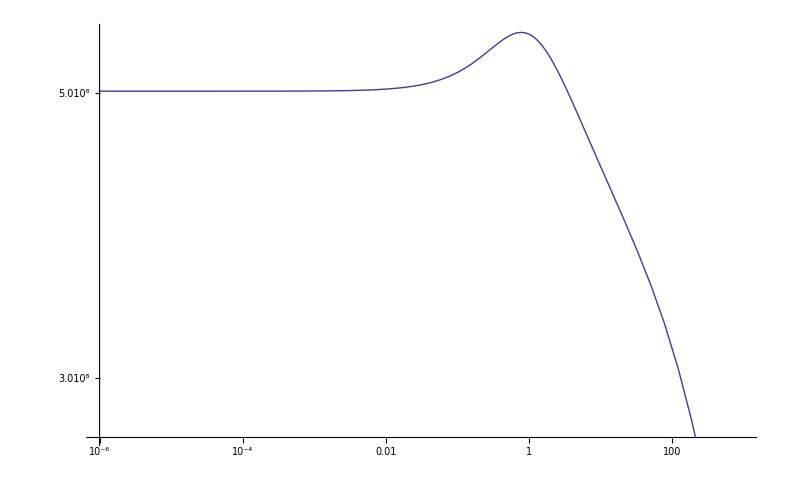

InterpolatingFunction::dmval: Input value {-13.8152} lies outside the range of data in the interpolating function. Extrapolation will be used.

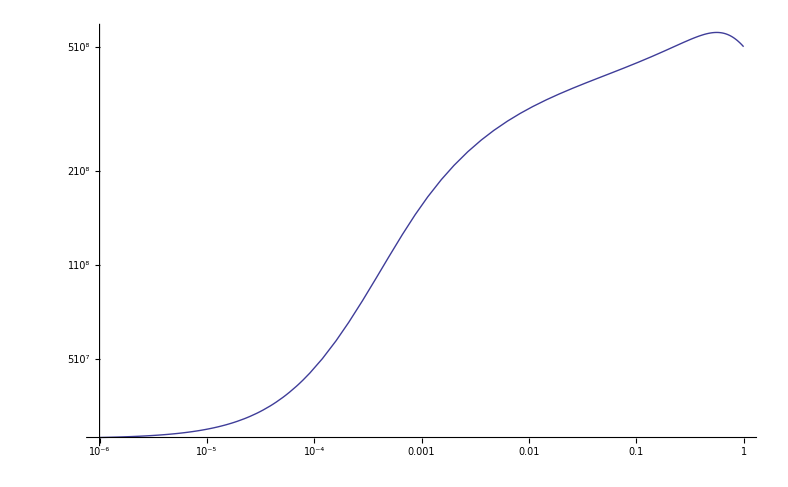

```mathematica
LogLogPlot[Gd1[1/(1+z)]/.s12,{z,0.000001,1000}]
LogLogPlot[Gd1[a]/.s12,{a,0.000001,1}]
```

InterpolatingFunction::dmval: Input value {-0.0951244} lies outside the range of data in the interpolating function. Extrapolation will be used.

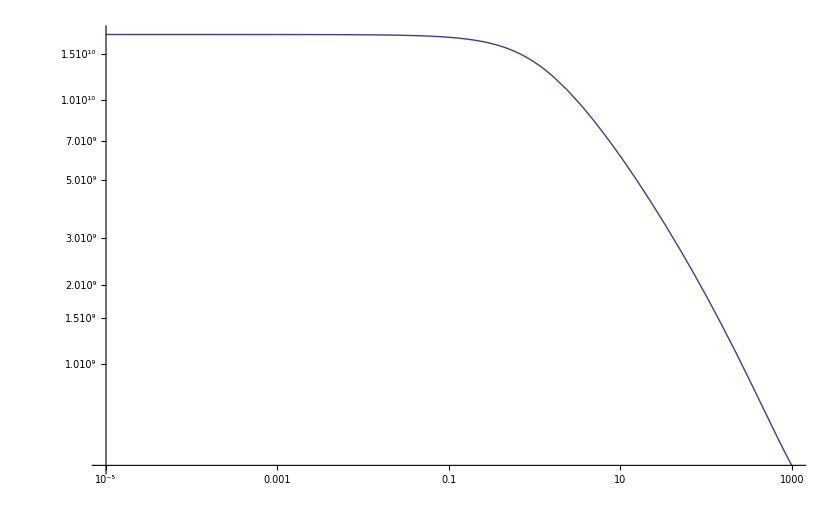

InterpolatingFunction::dmval: Input value {-6.90761} lies outside the range of data in the interpolating function. Extrapolation will be used.

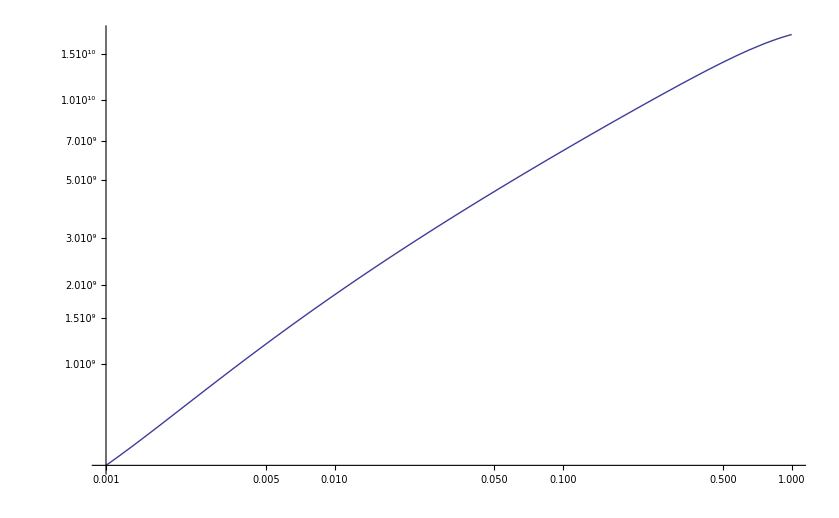

```mathematica
LogLogPlot[Gm1[1/(1+z)]/.s12,{z,0.00001,1000}]
LogLogPlot[Gm1[a]/.s12,{a,0.001,1},PlotRange->Full]
```

```mathematica
Export["DEInteracting\\2012-02-01\\growtest.xls",Growth1,"XLS"]
```

```mathematica
frac1=1/(((Growth1[[1]][1])/(Growth1[[1]][aokTabDE1[[nort1]]]))/(GrowthL[1]/GrowthL[aokTabL[[nort1]]]))
```

Part::partd: Part specification aokTabDE1 ⟦ 115 ⟧ is longer than depth of object.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.140609}. NIntegrate obtained 1.40265  + 1.42474\ ⅈ
 and 1.00955 for the integral and error estimates.

Part::partd: Part specification aokTabL ⟦ 115 ⟧ is longer than depth of object.

NIntegrate::nlim: x = aokTabL ⟦ 115 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::partd: Part specification aokTabDE1 ⟦ 115 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

((1.40271+1.4248 ⅈ) {InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}[aokTabDE1⟦115⟧])/(NIntegrate[1/(iHL[x]/HL0)^3,{x,0,aokTabL⟦115⟧}] √(0.73+0.0000809/aokTabL⟦115⟧^4+0.27/aokTabL⟦115⟧^3) {InterpolatingFunction[{{0.001,1.}},<>][x],InterpolatingFunction[{{0.001,1.}},<>][x]}[1])

```mathematica
LogLogPlot[Growth1[[1]],{x,0.001,1}]
```

```mathematica
Clear[a]
N[GrowthL2[1/3201]]
λ1[a]
s12:=NDSolve[{Gm1''[a]+(2/a+mH1'[a]/mH1[a]+6δ2 λ1[a]/a)Gm1'[a]==(3δ2 λ1[a] 1/a^2(1+3w1+3δ2 (1+2λ1[a]))-3δ2 λ1[a] 1/a mH1'[a]/mH1[a]+3/2 1/a^2(Ωm0 a^-3+δ2/(δ2+w1)ΩDE0 a^-3(1-a^(-3(δ2+w1)))))Gm1[a] +(3δ2 λ1[a] 1/a^2(1-3(δ2+w1))+3δ2 λ1[a]/a mH1'[a]/mH1[a]+3/2 1/a^2 ΩDE0 a^(-3(δ2+1+w1)))Gd1[a]+3δ2 λ1[a]/a Gd1'[a],(a mH1[a])^2 Gd1''[a]== -(2+3 ce2 -3w1 -3 δ2/(w1+1)+a mH1'[a]/mH1[a]) a (mH1[a])^2 Gd1'[a]+(-3 ce2 a mH1'[a]/mH1[a]+3(δ2+w1)mH1'[a]/mH1[a] a-k1^2 ce2 (1/mH1[a])^2+3/2(1+w1)a^(-3(1+w1+δ2))+3(w1-ce2)(1-3 δ2/(1+w1))) mH1[a]Gd1[a],Gm1[1/3201]==2.725976446996827*^8,Gm1'[1/3201]==0,Gd1[1/3201]==(2.725976446996827*^8)/3,Gd1'[1/3201]==0},{Gm1,Gd1},{a,0.0001,1}]
Growth1:={Gm1[a],Gd1[a]}/.s12
LogLogPlot[Growth1,{a,0.001,1}]
```

```mathematica
solL:=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10000}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
s11:=NDSolve[{(a mH1[a])^2 D[D[Gd1[a],a],a]== -(2+3 ce2 -3w1 -3 δ2/(w1+1)+a D[mH1[a],a]/mH1[a]) a (mH1[a])^2 D[Gd1[a],a]+(-3 ce2 a D[mH1[a],a]/mH1[a]+3(δ2+w1)D[mH1[a],a]/mH1[a] a-k1^2 ce2 (1/mH1[a])^2+3/2(1+w1)a^(-3(1+w1+δ2))+3(w1-ce2)(1-3 δ2/(1+w1))) mH1[a]Gd1[a],Gd1[1/3201]==10^-9,Gd1'[1/3201]==0},Gd1,{a,0.001,10}]
Growthd1[a_]:=Gd1[a]/.s11[[1]]
s12:=NDSolve[{D[D[Gm1[a],a],a]+(2/a+D[mH1[a],a]/mH1[a]+6δ2 λ1[a]/a)D[Gm1[a],a]== (3δ2 λ1[a] 1/a^2(1+3w1+3δ2 (1+2λ1[a]))-3δ2 λ1[a] 1/a D[mH1[a],a]/mH1[a]+3/2 1/a^2(Ωm0 a^-3+δ2/(δ2+w1)ΩDE0 a^-3(1-a^(-3(δ2+w1)))))Gm1[a] +(3δ2 λ1[a] 1/a^2(1-3(δ2+w1))+3δ2 λ1[a]/a D[mH1[a],a]/mH1[a]+3/2 1/a^2 ΩDE0 a^(-3(δ2+1+w1)))Growthd1[a]+3δ2 λ1[a]/a Growthd1'[a],Gm1[10^-7]==N[GrowthL2[10^-7]],Gm1'[1/3201]==0},Gm1,{a,0.001,10}]
Growth1[a_]:=Gm1[a]/.sol1[[1]]
sol2:=NDSolve[{D[D[Gm2[a],a],a]+(2/a+D[mH2[a],a]/mH2[a]+6δ2 λ2[a]/a)D[Gm2[a],a]== (3δ2 λ2[a] 1/a^2(1+3w2+3δ2 (1+2λ2[a]))-3δ2 λ2[a] 1/a D[mH2[a],a]/mH2[a]+3/2 1/a^2(Ωm0 a^-3+δ2/(δ2+w2)ΩDE0 a^-3(1-a^(-3(δ2+w2)))))Gm2[a] +(3δ2 λ2[a] 1/a^2(1-3(δ2+w2))+3δ2 λ2[a]/a D[mH2[a],a]/mH2[a]+3/2 1/a^2 ΩDE0 a^(-3(δ2+1+w2)))Gd2[a]+3δ2 λ2[a]/a Gd2[a],(a mH2[a])^2 D[D[Gd2[a],a],a]== -(2+3 ce2 -3w2 -3 δ2/(w2+1)+a D[mH2[a],a]/mH2[a]) a (mH2[a])^2 D[Gd2[a],a]+(-3 ce2 a D[mH2[a],a]/mH2[a]+3(δ2+w2)D[mH2[a],a]/mH2[a] a-k2^2 ce2 (1/mH2[a])^2+3/2(1+w2)a^(-3(1+w2+δ2))+3(w2-ce2)(1-3 δ2/(1+w2)))mH2[a]Gd2[a],Gm2'[10^-7]==N[GrowthL2'[10^-7]],Gm2[10^-7]==N[GrowthL2[10^-7]]},{Gm2,Gd2},{a,0.001,10}]
Growth2[a_]:=Gm2[a]/.sol2[[1]]
```

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",30,Bold,Orange]]
(*********************************************)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*nort=197-tranzL*)
k1=PowerS[[nort1,1]]
k2=PowerS[[nort2,1]]
N[GrowthL2[1/3201]]
fracs=1/((Growths[1]/Growths[aokTabs[[norts]]])/(GrowthL[1]/GrowthL[aokTabL[[norts]]]))
N[Gm1[aokTabDE1[[nort1]]]]
nort1
Growthd1[[aokTabDE1[[nort1]]]]
frac1=1/((Growth1[1]/Growth1[aokTabDE1[[nort1]]])/(GrowthL[1]/GrowthL[aokTabL[[nort1]]]))
frac2=1/((Growth2[1]/Growth2[aokTabDE2[[nort2]]])/(GrowthL[1]/GrowthL[aokTabL[[nort2]]]))
```

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",30,Bold,Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {5,0},PlotStyle->{Orange}]
```

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a]},{a,10^-4,1},PlotStyle->{Purple,Red,Black,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{Growths[a]/a,GrowthL[a]/a,GrowthDE2[a]/a,GrowthDE3[a]/a},{a,10^-4,1},PlotStyle->{Purple,Red,Black,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",30,Bold,Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];
Lambdas[mn_]:=dHs[1/mn];LambdaL[mn_]:=dHL[1/mn];Lambda2[mn_]:=dH2[1/mn];Lambda3[mn_]:=dH3[1/mn];
```

```mathematica
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{mn GrowthDE2[1/mn],mn GrowthL3[1/mn],mn GrowthL[1/mn],mn GrowthL2[1/mn]},{mn,0.1,1000},PlotStyle->{Black,Blue,Red,Orange}]
```

```mathematica
(*********************************************)
Print[Style["Tables for Q factors",30,Bold,Orange]]
(*********************************************)
Qfactor2=Table[{PowerS[[i+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE2}];
Qfactor2Ex=Table[{PowerS[[i,1]],frac2(GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])},{i,1,tranzDE2}];
Qfac2=Join[Qfactor2Ex,Qfactor2];
Qfactor2[[1]]
Qfactor2[[1]][[1]]
Qfactor3=Table[{PowerS[[i+tranzDE3,1]],frac3 (GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE3}];
Qfactor3Ex=Table[{PowerS[[i,1]],frac3(GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])},{i,1,tranzDE3}];
Qfac3=Join[Qfactor3Ex,Qfactor3];
Qfactor3[[1]]
Qfactor3[[1]][[1]]
(*********************************************)
Print[Style["Export the Q factors",30,Bold,Orange]]
(*********************************************)
Export["DEInteracting\\2012-02-01\\QfactorDE3vsL.xls",Qfac3,"XLS"]
```

```mathematica
(GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])
Qfactor3[[1]]
Qfactor3Ex[[tranzDE3]]
frac3
```

```mathematica
(*********************************************)
Print[Style["Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.",30,Bold,Orange]]
(*********************************************)

(*********************************************)
Print[Style["Construct the normalized power spectrum (different units) and export them",30,Bold,Orange]]
(*********************************************)
PowerSS=Table[{PowerS[[i,1]],PowerS[[i,2]]},{i,1,leth}];
PowerSDE2=Table[{PowerSS[[i,1]],(Qfac2[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
PowerSDE3=Table[{PowerSS[[i,1]],(Qfac3[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
ListLogLogPlot[PowerS]
ListLogLogPlot[PowerSS]
(*********************************************)
Print[Style["Export power spectrum raw data",30,Bold,Orange]]
(*********************************************)
Export["DEInteracting\\2012-02-01\\PowerSScale.xls",PowerSS,"XLS"]
Export["DEInteracting\\2012-02-01\\PowerSDE2.xls",PowerSDE2,"XLS"]
Export["DEInteracting\\2012-02-01\\PowerSDE3.xls",PowerSDE3,"XLS"]
```

```mathematica
(*********************************************)
Print[Style["Import the Q factors calculated previously.",30,Bold,Orange]]
(*********************************************)
QfDe2VsL=Import["CPL\\CPL_SychronousGauge_2012-01-10\\QfactorDE2vsL.xls"];
QfDe3VsL=Import["CPL\\CPL_SychronousGauge_2012-01-10\\QfactorDE3vsL.xls"];
(*********************************************)
Print[Style["Plot P(k)",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3},Joined->True,AxesLabel->{k,P},PlotRange->Automatic,PlotStyle->{Red,Black,Blue},PlotLegend->{"LCDM","w2","w3"},LegendPosition->{1.1,-0.4}]
(*********************************************)
Print[Style["Plot Qfactors vs k",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{QfDe2VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w2"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{QfDe3VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w3"},LegendPosition->{1.1,-0.4}]
```